# Constant Calculation

```mathematica
(* Constant *)
kB = 1.3806504 10^-23 J K^-1 ;
e = 1.602176487 10^-19 C;
ℏ=1.054571628 10^-34 J s;
c=299792458 m s^-1;
me=9.10938215 10^-31 kg;
mn=1.67492729 10^-27 kg;
mp=1.672621637 10^-27 kg;
gp=5.585694713;
ge=-2.00231904622;
μ0=4 π 10^-7 kg/(m s^2); (* H/m *)
ϵ0= 1/(μ0 c^2)//N;
NA=6.022141 10^23 mol^-1;
```

```mathematica
(*Composite constant*)
α=e^2/((4π ϵ0)ℏ c);
a=ℏ/(me c α);
μB= (e ℏ)/(2 me);
μN=(e ℏ)/(2mp);
μe=ge μB 1/2; (*ge μB S/ℏ , where <Sz> = ℏ/2 *)
μp=gp μN 1/2 ;
γee=ge e/(2me)
γe=(2μe)/(ℏ 10^6)1/(2π)(* 2π 10^6 convert s^-1 to MHz *)
γpp=gp e/(2 mp) 
γp=(2μp)/(ℏ  10^6)1/(2π)
```

-(1.76086×10^11 C)/kg

-(28025. C)/kg

(2.67522×10^8 C)/kg

(42.5775 C)/kg

```mathematica
Table[ Tanh[(μp 0.3)/(kB T K) kg/(C s)],{T,100,300,100}]
```

{3.06509×10^-6,1.53255×10^-6,1.0217×10^-6}

```mathematica
γe/γp
```

-658.211

```mathematica
(μ0 γe γp)/(4π)ℏ/(10^-33 m^3) m^2 s^2/C^2 (kg m^2 s^-2)/J 1/(2π 10^9)
```

-79.0644/s

```mathematica
Solve[γγp B==12.6]
```

```mathematica
(* C = m s *)
(* Tesla = kg / ( C s) *)
```

```mathematica
(* Unit Convertor the input need *)
kg2MeV[x_]:=(x/kg)c^2/e(C s^2/m^2)1/10^6 MeV
T2Basic[x_]:=(x /T )((s C)/kg)  
J2eV[x_]:=(x/e )(C  eV/J)  ; eV2J[x_]:=(x e )/(C  eV/J) 
J2MeV[x_]:=(x/e)(C  MeV/J) 10^-6 ;MeV2J[x_]:=(x e )/(C  MeV/J) 10^6 
nλ2f[λ_]:= c / (λ 10^-9 m)nm Hz s//N;f2nλ[f_]:= c/f nm/10^-9 Hz s/m //N
f2J[f_]:=ℏ 2π f 1/(Hz s)//N ; J2f[x_]:= x/(ℏ 2 π)Hz s
kg2J[x_]:=x c^2 ( J s^2/(m^2 kg))
ThermalK2eV[t_]:=t kB/e  (C eV)/J;eV2ThermalK[ev_]:=ev e/kB J/(C eV);
eV2nλ[ev_]:=f2nλ[J2f[eV2J[ev]]]; nλ2eV[λ_]:=J2eV[f2J[nλ2f[λ]]];
nm2fm[x_]:=x 1000000 fm/nm;
Hz2GHz[f_]:=f/10^9 GHz/Hz;
```

```mathematica
μs2kHz[t_]:=N[1/t]μs 10^3 kHz;
kHz2μs[f_]:=N[1/f]kHz 10^3 μs;
```

## Sand box

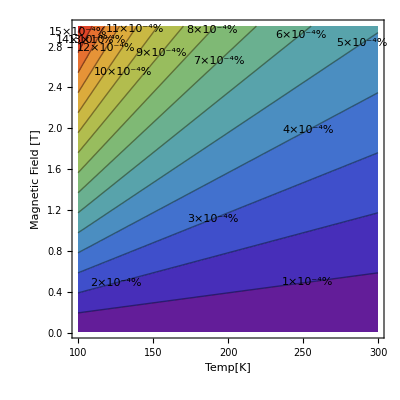

```mathematica
ContourPlot[Tanh[μp (B kg)/(2 kB C K s T)]1000000,{T,100,300},{B,0.01,3},ColorFunction->"Rainbow",ContourLabels->Function[{x,y,z},Text[Style[ToString[z]<>"×10^-4%",Medium],{x,y}]],Contours->Function[{min,max},Range[min,max,1]],
FrameLabel->{Style["Temp[K]",Medium],Style["Magnetic Field [T]",Medium]},ImageSize->400]
```

```mathematica
Tanh[μp (B kg)/(kB C K s T)]/.{B->1.8,T->1.2}
```

0.00153254

```mathematica
Clear[T]
```

```mathematica
KE=240 10^6  e/C
Mp=mp c^2/e MeV/10^6 C s^2/(kg m^2 cc^2)
```

3.84522×10^-11

(938.272 MeV)/cc^2

```mathematica
mp c^2/e
```

(9.38272×10^8 kg m^2)/(C s^2)

```mathematica
ℏ/e C/J eV
```

6.58212×10^-16 eV s

```mathematica
(J m)/(ℏ c)√(KE^2+2KE mp/kg (c/(m/s))^2) 10^-15 24^(1/3)1/2
```

5.20923

```mathematica
3.163029293996444*^10 √(4.81703127388277*^-23)
```

0.21953

```mathematica
24^(1/3)1/2//N
```

1.44225

```mathematica
((4.81703127388277*^-23)/(2.5669694954956602*^-26))^-1
```

0.000532895

```mathematica
Series[(J m)/(ℏ c)√(KE^2+2KE (m mp)/kg (c/(m/s))^2) 10^-15,{x,0,5}]
```

0.21953 √m √x+(0.000058493 x^(3/2))/(√m)-(7.79265×10^-9 x^(5/2))/m^(3/2)+(2.07633×10^-12 x^(7/2))/m^(5/2)-(6.91541×10^-16 x^(9/2))/m^(7/2)+O[x]^(11/2)

```mathematica
0.2195 √1000
```

6.9412

```mathematica
ℏ 2π 9 10^9/(kB 300)
```

0.00143977 K s

```mathematica
μs2kHz[56 μs]
kHz2μs[3.5kHz]
```

17.8571 kHz

285.714 μs

```mathematica
55/285.714
```

0.1925

```mathematica
f2nλ[h 10^6 Hz](10^-9 m)/nm
```

(299.792 m)/h

```mathematica
nλ2f[k 10^9 nm] MHz/(10^6 Hz)
```

(299.792 MHz)/k

```mathematica
k2G[10000]
```

0.01 ×10^6

```mathematica
J2f[eV2J[1eV]]
Hz2GHz[J2f[eV2J[1eV]]]
```

2.41799×10^14 Hz

241799. GHz

```mathematica
nm2fm[eV2nλ[10^9 eV]]
```

1.23984 fm

```mathematica
nλ2eV[1234 nm]
```

1.00473 eV

```mathematica
0.0002 γp
```

(0.0085155 C)/kg